## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/b20/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

maximum memory: 1.22156 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 6, 2020, time: 23:38:12

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/b20/apr-scraper-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 1.22156 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## 0 conversion

```mathematica
c=299792458;
```

```mathematica
(* 30 MHz *)
```

```mathematica
c/30000000//N
```

9.99308

```mathematica
(* 3 MHz *)
```

```mathematica
c/3000000//N
```

99.9308

```mathematica
c/50//N
```

5.99585×10^6

```mathematica
c/20//N
```

1.49896×10^7

## 1 read E fields from *.txt file

```mathematica
file="sphereCoarse.4112";
```

```mathematica
file="sphereFine.4112";
```

```mathematica
file="sphereSuperFine.4112";
file="PTW.4112";
file="repaired-mesh.4112"
```

repaired-mesh.4112

```mathematica
file="B20-standard-0.01m.4112";
```

### point to file

```mathematica
dirMoM="/Users/dantopa/Dropbox/2nd-generation/RCS-project/linux/ubuntu/";
```

```mathematica
dirMoM=dirData;
```

### read file to scan for data sets

```mathematica
dirMoM<>file<>".txt"
```

/Users/dantopa/Mathematica_files/io/ert/mercury/b20/data/B20-standard-0.01m.4112.txt

```mathematica
Import[dirData<>"A.txt","Data"]
```

{ ,---| Run Date: April      6, 2020;    Time: 23:13:26, , MM SIE VIE,14835, ,--------------------------------------------------------------------------------,                  ---| Mercury MOM Completed Sucessfully |---,--------------------------------------------------------------------------------}
 |  |  |  |

```mathematica
strmList=Import[dirData<>"A.txt","Data"];
title="B20 Airframe";
Λ=Dimensions[strmList]
```

{14843}

## 2 find table

### tag data sets: record line numbers

```mathematica
(* each data set represents a unique frequency *)
```

```mathematica
census={};
Table[
If[StringContainsQ[strmList[[k]],"Theta, Phi, Theta-Theta"],AppendTo[census,k]]
,{k,Length[strmList]}];
census
m=Length[census]
```

{492,1006,1520,2034,2548,3062,3576,4090,4604,5118,5632,6146,6660,7174,7688,8202,8716,9230,9744,10258,10772,11286,11800,12314,12828,13342,13856,14370}

28

#### empty containers for E field values

```mathematica
θθ={};
θϕ={};
ϕθ={};
ϕϕ={};
```

### harvest frequencies

```mathematica
frequencies={};
Table[
If[StringContainsQ[strmList[[k]],"Freq   ="],AppendTo[frequencies,StringSplit[strmList[[k]]]]]
,{k,Length[strmList]}];
frequencies
```

{{Freq,=,3.00E+00,MHz},{Freq,=,4.00E+00,MHz},{Freq,=,5.00E+00,MHz},{Freq,=,6.00E+00,MHz},{Freq,=,7.00E+00,MHz},{Freq,=,8.00E+00,MHz},{Freq,=,9.00E+00,MHz},{Freq,=,10.00E+00,MHz},{Freq,=,11.00E+00,MHz},{Freq,=,12.00E+00,MHz},{Freq,=,13.00E+00,MHz},{Freq,=,14.00E+00,MHz},{Freq,=,15.00E+00,MHz},{Freq,=,16.00E+00,MHz},{Freq,=,17.00E+00,MHz},{Freq,=,18.00E+00,MHz},{Freq,=,19.00E+00,MHz},{Freq,=,20.00E+00,MHz},{Freq,=,21.00E+00,MHz},{Freq,=,22.00E+00,MHz},{Freq,=,23.00E+00,MHz},{Freq,=,24.00E+00,MHz},{Freq,=,25.00E+00,MHz},{Freq,=,26.00E+00,MHz},{Freq,=,27.00E+00,MHz},{Freq,=,28.00E+00,MHz},{Freq,=,29.00E+00,MHz},{Freq,=,30.00E+00,MHz}}

### reader

```mathematica
nAngles=360;
```

```mathematica
Do[
myLine=census[[k]]+1;
fields=Table[
str=StringSplit[strmList[[myLine+j]]];
str=StringReplace[#,","->""]&/@str;
str=StringReplace[#,"("->""]&/@str;
str=StringReplace[#,")"->""]&/@str;
str=StringReplace[#,"{"->""]&/@str;
str=StringReplace[#,"}"->""]&/@str;
tbl=Read[StringToStream[#],Number]&/@Flatten[str]
,{j,nAngles}];
AppendTo[θθ,fields[[All,3]]+ⅈ fields[[All,4]]];
AppendTo[θϕ,fields[[All,5]]+ⅈ fields[[All,6]]];
AppendTo[ϕθ,fields[[All,7]]+ⅈ fields[[All,8]]];
AppendTo[ϕϕ,fields[[All,9]]+ⅈ fields[[All,10]]];
,{k,m}];
```

## 3 combine electric fields

### rcs

```mathematica
meanRCS=1/2(Abs[θθ]+Abs[θϕ]+Abs[ϕθ]+Abs[ϕϕ]);
```

### polarizations

```mathematica
RR=((θθ-ϕϕ)-ⅈ(θϕ+ϕθ))/2;
RL=((θθ+ϕϕ)-ⅈ(θϕ-ϕθ))/2;LR=((θθ+ϕϕ)+ⅈ(θϕ-ϕθ))/2;LL=((θθ-ϕϕ)+ⅈ(θϕ+ϕθ))/2;
```

## 4 plot values

```mathematica
magRCS=Map[Abs,meanRCS,1];
argRCS=Map[Arg,meanRCS,1];
reRCS=Map[Re,meanRCS,1];
imRCS=Map[Im,meanRCS,1];
```

```mathematica
magRR=Map[Abs,RR,1];
argRR=Map[Arg,RR,1];
reRR=Map[Re,RR,1];
imRR=Map[Im,RR,1];
```

```mathematica
magRL=Map[Abs,RL,1];
argRL=Map[Arg,RL,1];
reRL=Map[Re,RL,1];
imRL=Map[Im,RL,1];
```

```mathematica
magLR=Map[Abs,LR,1];
argLR=Map[Arg,LR,1];
reLR=Map[Re,LR,1];
imLR=Map[Im,LR,1];
```

```mathematica
magLL=Map[Abs,LL,1];
argLL=Map[Arg,LL,1];
reLL=Map[Re,LL,1];
imLL=Map[Im,LL,1];
```

## 5 table of extrema

### rcs

```mathematica
Max[meanRCS]
```

6.83956×10^6

```mathematica
Min[meanRCS]
```

18188.5

### magnitude

```mathematica
fRR=Flatten[magRR];
fRL=Flatten[magRL];
fLR=Flatten[magLR];
fLL=Flatten[magLL];
```

```mathematica
extrema=TableForm[
{{Max[fRR],Max[fRL],Max[fLR],Max[fLL]},{Min[fRR],Min[fRL],Min[fLR],Min[fLL]}},
,TableHeadings->{{"max","min"},{"RR","RL","LR","LL"}}]
```

| RR | RL | LR | LL
max | 6.09765×10^6 | 4.73488×10^6 | 4.73477×10^6 | 5.52779×10^6
min | 982.03 | 1573.69 | 1573.04 | 856.233

### argument

```mathematica
fRR=Flatten[argRR];
fRL=Flatten[argRL];
fLR=Flatten[argLR];
fLL=Flatten[argLL];
```

```mathematica
extrema=TableForm[
{{Max[fRR],Max[fRL],Max[fLR],Max[fLL]},{Min[fRR],Min[fRL],Min[fLR],Min[fLL]}},
,TableHeadings->{{"max","min"},{"RR","RL","LR","LL"}}]
```

| RR | RL | LR | LL
max | 3.14138 | 3.14118 | 3.14124 | 3.1414
min | -3.1408 | -3.14146 | -3.14148 | -3.14099

```mathematica
{{, "RR", "RL", "LR", "LL"}, {"max", 3.1415528702479496, 3.140848818197667, 3.14080489554447, 3.140443012400203}, {"min", -3.138755801236539, -3.1407918103511663, -3.1406073882159222, -3.1415782385580937}}
```

{{3.14155,3.14085,3.1408,3.14044},{-3.13876,-3.14079,-3.14061,-3.14158}}

### re

```mathematica
fRR=Flatten[reRR];
fRL=Flatten[reRL];
fLR=Flatten[reLR];
fLL=Flatten[reLL];
```

```mathematica
extrema=TableForm[
{{Max[fRR],Max[fRL],Max[fLR],Max[fLL]},{Min[fRR],Min[fRL],Min[fLR],Min[fLL]}},
,TableHeadings->{{"max","min"},{"RR","RL","LR","LL"}}]
```

| RR | RL | LR | LL
max | 4.96089×10^6 | 4.01168×10^6 | 4.01162×10^6 | 4.27161×10^6
min | -5.70025×10^6 | -4.65689×10^6 | -4.65679×10^6 | -4.98508×10^6

```mathematica
{{, "RR", "RL", "LR", "LL"}, {"max", 52.32153, 0.9410299, 0.9410397, 80.08397}, {"min", -37.56739, -0.7295779, -0.7295754, -74.57554}}
```

{{52.3215,0.94103,0.94104,80.084},{-37.5674,-0.729578,-0.729575,-74.5755}}

### im

```mathematica
fRR=Flatten[imRR];
fRL=Flatten[imRL];
fLR=Flatten[imLR];
fLL=Flatten[imLL];
```

```mathematica
extrema=TableForm[
{{Max[fRR],Max[fRL],Max[fLR],Max[fLL]},{Min[fRR],Min[fRL],Min[fLR],Min[fLL]}},
,TableHeadings->{{"max","min"},{"RR","RL","LR","LL"}}]
```

| RR | RL | LR | LL
max | 6.0945×10^6 | 3.75535×10^6 | 3.75541×10^6 | 4.20811×10^6
min | -3.96683×10^6 | -3.4327×10^6 | -3.43269×10^6 | -4.70832×10^6

```mathematica
{{, "RR", "RL", "LR", "LL"}, {"max", 52.7232, 0.8522636, 0.852276, 70.43282}, {"min", -37.82338, -0.8079512, -0.807952, -81.63143}}
```

{{52.7232,0.852264,0.852276,70.4328},{-37.8234,-0.807951,-0.807952,-81.6314}}

## 6 plot E fields

```mathematica
νticks={{1,3},{8,10},{18,20},{28,30}};
λticks={{1,100},{15,20},{4,50},{28,10}};θticks={{1,0},{91,π/4},{181,π/2},{271,(3π)/4},{361,2π}};
θticks={{1,0},{91,90},{181,180},{271,270},{361,360}};
```

### plot utility

```mathematica
Clear[myPlot];
myPlot[ψ_,str_String,options___]:=Module[{g},
g=ArrayPlot[ψ,
options,
ColorFunction->(Hue[(1-# )magicnumber]&),
FrameTicks->{{{1,3},15,20,{28,30}},{0,90,180,270,360},{{1,100},{4,50},{13,20},{28,10}},None},
FrameLabel->{"Frequency MHZ","Angle","Wavelength m",None},
PlotLabel->title<>lf<>str,
AspectRatio->3/4,
PlotLegends->Placed[Automatic,After]]]
```

### rcs

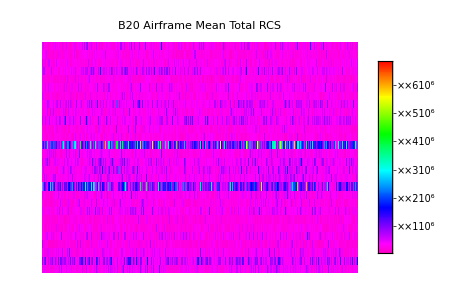

```mathematica
g000=myPlot[meanRCS,"Mean Total RCS"]
```

### magnitude

```mathematica
g001=myPlot[magRR,"Energy Magnitude (RR)"];
g002=myPlot[magRL,"Energy Magnitude (RL)"];
g003=myPlot[magLR,"Energy Magnitude (LR)"];
g004=myPlot[magLL,"Energy Magnitude (LL)"];
```

### argument

```mathematica
g101=myPlot[argRR,"Complex Argument (RR)"];
g102=myPlot[argRL,"Complex Argument (RL)"];
g103=myPlot[argLR,"Complex Argument (LR)"];
g104=myPlot[argLL,"Complex Argument (LL)"];
```

### real part

```mathematica
g201=myPlot[reRR,"Real Part (RR)"];
g202=myPlot[reRL,"Real Part (RL)"];
g203=myPlot[reLR,"Real Part (LR)"];
g204=myPlot[reLL,"Real Part (LL)"];
```

### imaginary part

```mathematica
g301=myPlot[imRR,"Imaginary Part (RR)"];
g302=myPlot[imRL,"Imaginary Part (RL)"];
g303=myPlot[imLR,"Imaginary Part (LR)"];
g304=myPlot[imLL,"Imaginary Part (LL)"];
```

## 7 export

```mathematica
tresExport[title<>" rcs",g000]
```

```mathematica
tresExport[title<>" RR-mag",g001];
tresExport[title<>" RL-mag",g002];
tresExport[title<>" LR-mag",g003];
tresExport[title<>" LL-mag",g004];
```

```mathematica
Clear[g001];
Clear[g002];
Clear[g003];
Clear[g004];
```

### magnitude

```mathematica
tresExport[title<>" RR-mag",g001];
tresExport[title<>" RL-mag",g002];
tresExport[title<>" LR-mag",g003];
tresExport[title<>" LL-mag",g004];
```

```mathematica
Clear[g001,g002,g003,g004];
```

### argument

```mathematica
tresExport[title<>" RR-arg",g101];
tresExport[title<>" RL-arg",g102];
tresExport[title<>" LR-arg",g103];
tresExport[title<>" LL-arg",g104];
```

```mathematica
Clear[g101,g102,g103,g104];
```

### re

```mathematica
tresExport[title<>" RR-re",g201];
tresExport[title<>" RL-re",g202];
tresExport[title<>" LR-re",g203];
tresExport[title<>" LL-re",g204];
```

```mathematica
Clear[g201,g202,g203,g204];
```

### im

```mathematica
tresExport[title<>" RR-im",g301];
tresExport[title<>" RL-im",g302];
tresExport[title<>" LR-im",g303];
tresExport[title<>" LL-im",g304];
```

```mathematica
Clear[g301,g302,g303,g304];
```

## transition matrix

```mathematica
M={{1,-1,-ⅈ,1},{1,1,-ⅈ,-1},{1,1,ⅈ,-1},{1,-1,ⅈ,1}};
```

```mathematica
M//mf
```

(1 | -1 | -ⅈ | 1
1 | 1 | -ⅈ | -1
1 | 1 | ⅈ | -1
1 | -1 | ⅈ | 1)

```mathematica
8PseudoInverse[M]
```

{{2,2,2,2},{-1,1,1,-1},{2 ⅈ,2 ⅈ,-2 ⅈ,-2 ⅈ},{1,-1,-1,1}}

```mathematica
NullSpace[M†]
```

{{-1,1,-1,1}}

```mathematica
NullSpace[M]
```

{{0,1,0,1}}

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```